```mathematica
{ol500c24h,ol500c24hkeep,ol500c24hkill,ol500c24hmem,oltyp}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\ol500c24htest.mx"];
```

```mathematica
{hypgen1,hypgen8,hypgen16,hyp1keep,hyp8keep,hyp16keep,hyp1mem,hyp8mem,hyp16mem,hypkill1,hypkill8,hypkill16}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hyp500c24htest.mx"];
```

```mathematica
{hyptyp2,hyptyp3,hyptyp4,hyptyp5,hyptyp6,hyptyp7,hyptyp9,hyptyp10,hyptyp11,hyptyp12,hyptyp13,hyptyp14,hyptyp15}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hyptyp.mx"];
```

```mathematica
{hyptyp1,hyptyp8,hyptyp16}=Parallelize[{titeryieldproductivity[hypkill1],titeryieldproductivity[hypkill8],titeryieldproductivity[hypkill16]}];
```

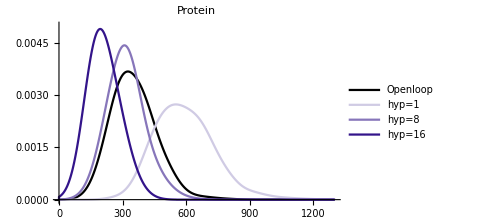

```mathematica
SmoothHistogram[{ol500c24h[[1]][[1]]/ol500c24h[[1]][[6]],hypgen1[[1]][[1]]/hypgen1[[1]][[6]],hypgen8[[1]][[1]]/hypgen8[[1]][[6]],hypgen16[[1]][[1]]/hypgen16[[1]][[6]]},50,PlotRange->{{0,1300},{0,0.005}},PlotLegends->{"Openloop","hyp=1","hyp=8","hyp=16"},PlotLabel->Style["Protein",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#d0cbe4"],Thick],Directive[RGBColor["#8776ba"],Thick],Directive[RGBColor["#33148a"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

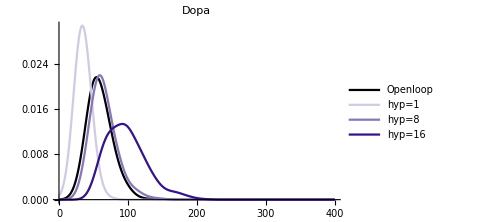

```mathematica
SmoothHistogram[{ol500c24h[[1]][[3]]/ol500c24h[[1]][[6]],hypgen1[[1]][[3]]/hypgen1[[1]][[6]],hypgen8[[1]][[3]]/hypgen8[[1]][[6]],hypgen16[[1]][[3]]/hypgen16[[1]][[6]]},10,PlotRange->{{0,400},Automatic},PlotLegends->{"Openloop","hyp=1","hyp=8","hyp=16"},PlotLabel->Style["Dopa",Black,16],
PlotStyle->{Directive[Black],Directive[RGBColor["#d0cbe4"],Thick],Directive[RGBColor["#8776ba"],Thick],Directive[RGBColor["#33148a"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

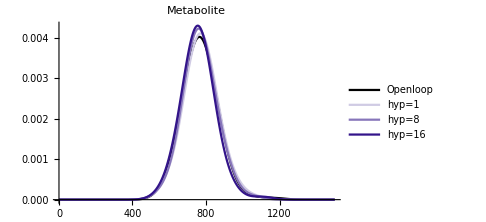

```mathematica
SmoothHistogram[{ol500c24h[[1]][[4]]/ol500c24h[[1]][[6]],hypgen1[[1]][[4]]/hypgen1[[1]][[6]],hypgen8[[1]][[4]]/hypgen8[[1]][[6]],hypgen16[[1]][[4]]/hypgen16[[1]][[6]]},50,PlotRange->{{0,1500},Automatic},PlotLegends->{"Openloop","hyp=1","hyp=8","hyp=16"},PlotLabel->Style["Metabolite",Black,16],
PlotStyle->{Directive[Black],Directive[RGBColor["#d0cbe4"],Thick],Directive[RGBColor["#8776ba"],Thick],Directive[RGBColor["#33148a"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

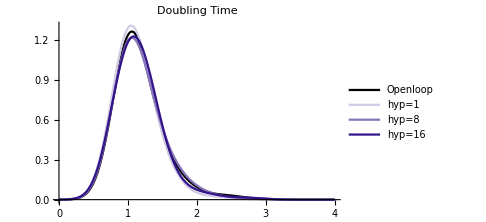

```mathematica
SmoothHistogram[{Log[2]/ol500c24h[[1]][[5]],Log[2]/hypgen1[[1]][[5]],Log[2]/hypgen8[[1]][[5]],Log[2]/hypgen16[[1]][[5]]},0.2,PlotRange->{{0,4},Automatic},PlotLegends->{"Openloop","hyp=1","hyp=8","hyp=16"},PlotLabel->Style["Doubling Time",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#d0cbe4"],Thick],Directive[RGBColor["#8776ba"],Thick],Directive[RGBColor["#33148a"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

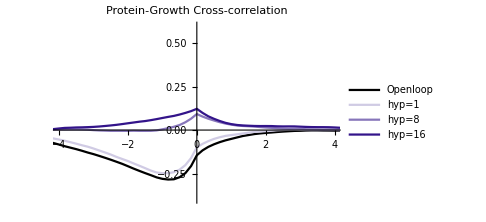

```mathematica
ListLinePlot[{ol500c24hmem[[4]],hyp1mem[[4]],hyp8mem[[4]],hyp16mem[[4]]},PlotRange->{{-4,4},{-0.4,0.6}},PlotLegends->{"Openloop","hyp=1","hyp=8","hyp=16"},PlotLabel->Style["Protein-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#d0cbe4"],Thick],Directive[RGBColor["#8776ba"],Thick],Directive[RGBColor["#33148a"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

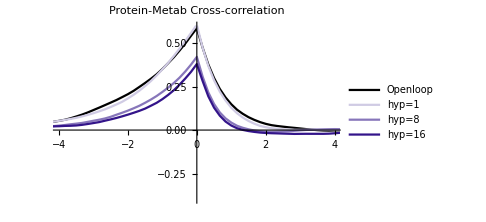

```mathematica
ListLinePlot[{ol500c24hmem[[6]],hyp1mem[[6]],hyp8mem[[6]],hyp16mem[[6]]},PlotRange->{{-4,4},{-0.4,0.6}},PlotLegends->{"Openloop","hyp=1","hyp=8","hyp=16"},PlotLabel->Style["Protein-Metab Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#d0cbe4"],Thick],Directive[RGBColor["#8776ba"],Thick],Directive[RGBColor["#33148a"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

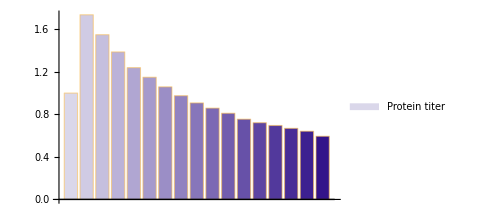

```mathematica
BarChart[{oltyp[[2]]/oltyp[[2]],hyptyp1[[2]]/oltyp[[2]],hyptyp2[[2]]/oltyp[[2]],hyptyp3[[2]]/oltyp[[2]],hyptyp4[[2]]/oltyp[[2]],hyptyp5[[2]]/oltyp[[2]],hyptyp6[[2]]/oltyp[[2]],hyptyp7[[2]]/oltyp[[2]],hyptyp8[[2]]/oltyp[[2]],hyptyp9[[2]]/oltyp[[2]],hyptyp10[[2]]/oltyp[[2]],hyptyp11[[2]]/oltyp[[2]],hyptyp12[[2]]/oltyp[[2]],hyptyp13[[2]]/oltyp[[2]],hyptyp14[[2]]/oltyp[[2]],hyptyp15[[2]]/oltyp[[2]],hyptyp16[[2]]/oltyp[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#dad7ea"],
RGBColor["#d0cbe4"],
RGBColor["#c5bfde"],
RGBColor["#bbb2d8"],
RGBColor["#b0a6d2"],
RGBColor["#a69acc"],
RGBColor["#9b8ec6"],
RGBColor["#9182c0"],
RGBColor["#8776ba"],
RGBColor["#7c69b4"],
RGBColor["#725dae"],
RGBColor["#6751a8"],
RGBColor["#5d45a2"],
RGBColor["#52399c"],
RGBColor["#482c96"],
RGBColor["#3d2090"],
RGBColor["#33148a"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

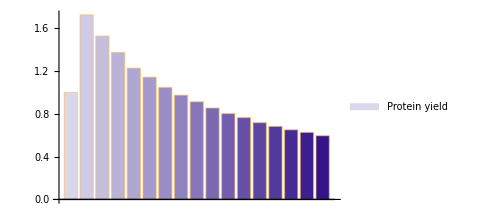

```mathematica
BarChart[{oltyp[[5]]/oltyp[[5]],hyptyp1[[5]]/oltyp[[5]],hyptyp2[[5]]/oltyp[[5]],hyptyp3[[5]]/oltyp[[5]],hyptyp4[[5]]/oltyp[[5]],hyptyp5[[5]]/oltyp[[5]],hyptyp6[[5]]/oltyp[[5]],hyptyp7[[5]]/oltyp[[5]],hyptyp8[[5]]/oltyp[[5]],hyptyp9[[5]]/oltyp[[5]],hyptyp10[[5]]/oltyp[[5]],hyptyp11[[5]]/oltyp[[5]],hyptyp12[[5]]/oltyp[[5]],hyptyp13[[5]]/oltyp[[5]],hyptyp14[[5]]/oltyp[[5]],hyptyp15[[5]]/oltyp[[5]],hyptyp16[[5]]/oltyp[[5]]},ChartLegends->{"Protein yield"},ChartStyle->{RGBColor["#dad7ea"],
RGBColor["#d0cbe4"],
RGBColor["#c5bfde"],
RGBColor["#bbb2d8"],
RGBColor["#b0a6d2"],
RGBColor["#a69acc"],
RGBColor["#9b8ec6"],
RGBColor["#9182c0"],
RGBColor["#8776ba"],
RGBColor["#7c69b4"],
RGBColor["#725dae"],
RGBColor["#6751a8"],
RGBColor["#5d45a2"],
RGBColor["#52399c"],
RGBColor["#482c96"],
RGBColor["#3d2090"],
RGBColor["#33148a"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

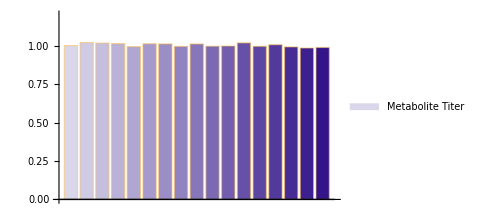

```mathematica
BarChart[{oltyp[[4]]/oltyp[[4]],hyptyp1[[4]]/oltyp[[4]],hyptyp2[[4]]/oltyp[[4]],hyptyp3[[4]]/oltyp[[4]],hyptyp4[[4]]/oltyp[[4]],hyptyp5[[4]]/oltyp[[4]],hyptyp6[[4]]/oltyp[[4]],hyptyp7[[4]]/oltyp[[4]],hyptyp8[[4]]/oltyp[[4]],hyptyp9[[4]]/oltyp[[4]],hyptyp10[[4]]/oltyp[[4]],hyptyp11[[4]]/oltyp[[4]],hyptyp12[[4]]/oltyp[[4]],hyptyp13[[4]]/oltyp[[4]],hyptyp14[[4]]/oltyp[[4]],hyptyp15[[4]]/oltyp[[4]],hyptyp16[[4]]/oltyp[[4]]},ChartLegends->{"Metabolite Titer"},PlotRange->{0,1.2},ChartStyle->{RGBColor["#dad7ea"],
RGBColor["#d0cbe4"],
RGBColor["#c5bfde"],
RGBColor["#bbb2d8"],
RGBColor["#b0a6d2"],
RGBColor["#a69acc"],
RGBColor["#9b8ec6"],
RGBColor["#9182c0"],
RGBColor["#8776ba"],
RGBColor["#7c69b4"],
RGBColor["#725dae"],
RGBColor["#6751a8"],
RGBColor["#5d45a2"],
RGBColor["#52399c"],
RGBColor["#482c96"],
RGBColor["#3d2090"],
RGBColor["#33148a"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

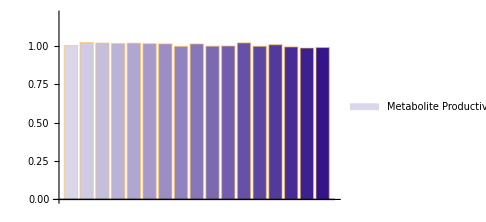

```mathematica
BarChart[{oltyp[[9]]/oltyp[[9]],hyptyp1[[9]]/oltyp[[9]],hyptyp2[[9]]/oltyp[[9]],hyptyp3[[9]]/oltyp[[9]],hyptyp4[[9]]/oltyp[[9]],hyptyp5[[9]]/oltyp[[9]],hyptyp6[[9]]/oltyp[[9]],hyptyp7[[9]]/oltyp[[9]],hyptyp8[[9]]/oltyp[[9]],hyptyp9[[9]]/oltyp[[9]],hyptyp10[[9]]/oltyp[[9]],hyptyp11[[9]]/oltyp[[9]],hyptyp12[[9]]/oltyp[[9]],hyptyp13[[9]]/oltyp[[9]],hyptyp14[[9]]/oltyp[[9]],hyptyp15[[9]]/oltyp[[9]],hyptyp16[[9]]/oltyp[[9]]},ChartLegends->{"Metabolite Productivity"},PlotRange->{0,1.2},ChartStyle->{RGBColor["#dad7ea"],
RGBColor["#d0cbe4"],
RGBColor["#c5bfde"],
RGBColor["#bbb2d8"],
RGBColor["#b0a6d2"],
RGBColor["#a69acc"],
RGBColor["#9b8ec6"],
RGBColor["#9182c0"],
RGBColor["#8776ba"],
RGBColor["#7c69b4"],
RGBColor["#725dae"],
RGBColor["#6751a8"],
RGBColor["#5d45a2"],
RGBColor["#52399c"],
RGBColor["#482c96"],
RGBColor["#3d2090"],
RGBColor["#33148a"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
{hypgen1,hypgen10,hypgen50,hypgen90,hypgen99,hypkeep1,hypkeep10,hypkeep50,hypkeep90,hypkeep99,hypmem1,hypmem10,hypmem50,hypmem90,hypmem99,hypkill1,hypkill10,hypkill50,hypkill90,hypkill99,hyptyp1,hyptyp10,hyptyp50,hyptyp90,hyptyp99}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hyp500c24hpercent.mx"];
```

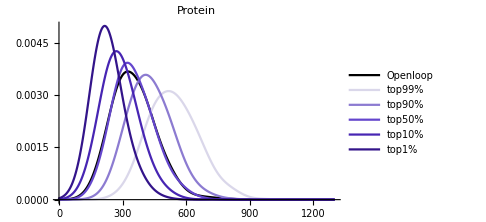

```mathematica
SmoothHistogram[{ol500c24h[[1]][[1]]/ol500c24h[[1]][[6]],hypgen1[[1]][[1]]/hypgen1[[1]][[6]],hypgen10[[1]][[1]]/hypgen10[[1]][[6]],hypgen50[[1]][[1]]/hypgen50[[1]][[6]],hypgen90[[1]][[1]]/hypgen90[[1]][[6]],hypgen99[[1]][[1]]/hypgen99[[1]][[6]]},50,PlotRange->{{0,1300},{0,0.005}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Protein",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#dad7ea"],Thick],Directive[RGBColor["#8c7bd1"],Thick],Directive[RGBColor["#6446cd"],Thick],Directive[RGBColor["#4725b3"],Thick],Directive[RGBColor["#33148a"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

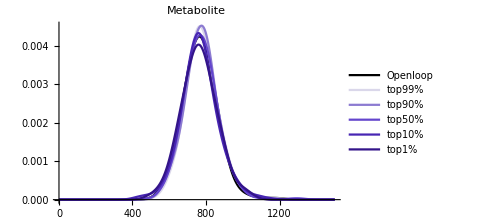

```mathematica
SmoothHistogram[{ol500c24h[[1]][[4]]/ol500c24h[[1]][[6]],hypgen1[[1]][[4]]/hypgen1[[1]][[6]],hypgen10[[1]][[4]]/hypgen10[[1]][[6]],hypgen50[[1]][[4]]/hypgen50[[1]][[6]],hypgen90[[1]][[4]]/hypgen90[[1]][[6]],hypgen99[[1]][[4]]/hypgen99[[1]][[6]]},40,PlotRange->{{0,1500},Automatic},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Metabolite",Black,16],
PlotStyle->{Directive[Black],Directive[RGBColor["#dad7ea"],Thick],Directive[RGBColor["#8c7bd1"],Thick],Directive[RGBColor["#6446cd"],Thick],Directive[RGBColor["#4725b3"],Thick],Directive[RGBColor["#33148a"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

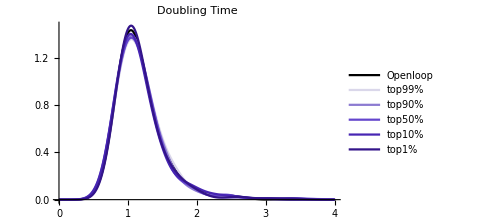

```mathematica
SmoothHistogram[{Log[2]/ol500c24h[[1]][[5]],Log[2]/hypgen1[[1]][[5]],Log[2]/hypgen10[[1]][[5]],Log[2]/hypgen50[[1]][[5]],Log[2]/hypgen90[[1]][[5]],Log[2]/hypgen99[[1]][[5]]},0.15,PlotRange->{{0,4},Automatic},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Doubling Time",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#dad7ea"],Thick],Directive[RGBColor["#8c7bd1"],Thick],Directive[RGBColor["#6446cd"],Thick],Directive[RGBColor["#4725b3"],Thick],Directive[RGBColor["#33148a"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

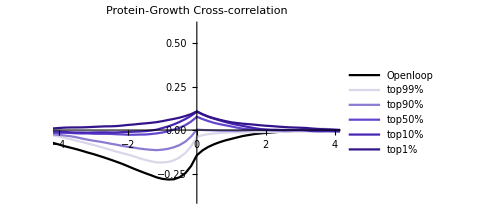

```mathematica
ListLinePlot[{ol500c24hmem[[4]],hypmem1[[4]],hypmem10[[4]],hypmem50[[4]],hypmem90[[4]],hypmem99[[4]]},PlotRange->{{-4,4},{-0.4,0.6}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Protein-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#dad7ea"],Thick],Directive[RGBColor["#8c7bd1"],Thick],Directive[RGBColor["#6446cd"],Thick],Directive[RGBColor["#4725b3"],Thick],Directive[RGBColor["#33148a"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

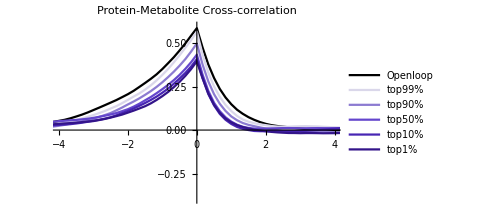

```mathematica
ListLinePlot[{ol500c24hmem[[6]],hypmem1[[6]],hypmem10[[6]],hypmem50[[6]],hypmem90[[6]],hypmem99[[6]]},PlotRange->{{-4,4},{-0.4,0.6}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Protein-Metabolite Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#dad7ea"],Thick],Directive[RGBColor["#8c7bd1"],Thick],Directive[RGBColor["#6446cd"],Thick],Directive[RGBColor["#4725b3"],Thick],Directive[RGBColor["#33148a"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

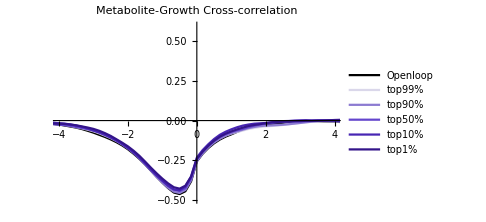

```mathematica
ListLinePlot[{ol500c24hmem[[5]],hypmem1[[5]],hypmem10[[5]],hypmem50[[5]],hypmem90[[5]],hypmem99[[5]]},PlotRange->{{-4,4},{-0.5,0.6}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Metabolite-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#dad7ea"],Thick],Directive[RGBColor["#8c7bd1"],Thick],Directive[RGBColor["#6446cd"],Thick],Directive[RGBColor["#4725b3"],Thick],Directive[RGBColor["#33148a"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

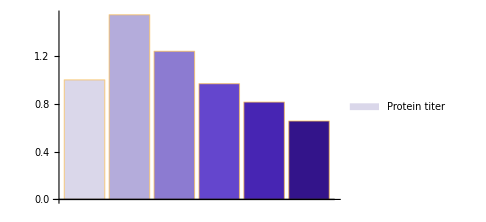

```mathematica
BarChart[{oltyp[[2]]/oltyp[[2]],hyptyp1[[2]]/oltyp[[2]],hyptyp10[[2]]/oltyp[[2]],hyptyp50[[2]]/oltyp[[2]],hyptyp90[[2]]/oltyp[[2]],hyptyp99[[2]]/oltyp[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#dad7ea"],
RGBColor["#b4acdb"],
RGBColor["#8c7bd1"],
RGBColor["#6446cd"],
RGBColor["#4725b3"],
RGBColor["#33148a"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

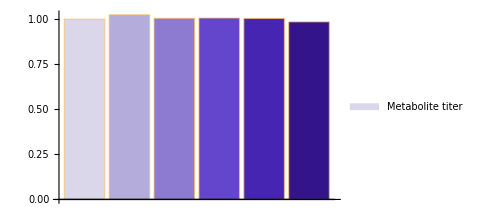

```mathematica
BarChart[{oltyp[[4]]/oltyp[[4]],hyptyp1[[4]]/oltyp[[4]],hyptyp10[[4]]/oltyp[[4]],hyptyp50[[4]]/oltyp[[4]],hyptyp90[[4]]/oltyp[[4]],hyptyp99[[4]]/oltyp[[4]]},ChartLegends->{"Metabolite titer"},ChartStyle->{RGBColor["#dad7ea"],
RGBColor["#b4acdb"],
RGBColor["#8c7bd1"],
RGBColor["#6446cd"],
RGBColor["#4725b3"],
RGBColor["#33148a"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

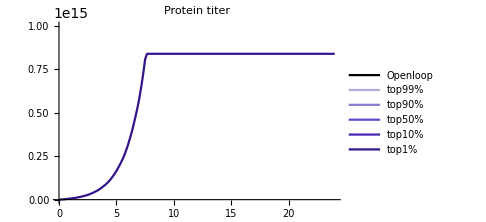

```mathematica
ListLinePlot[{oltyp[[1]],hyptyp1[[1]],hyptyp10[[1]],hyptyp50[[1]],hyptyp90[[1]],hyptyp99[[1]]},PlotLabel->"Protein titer",PlotStyle->{Black,
RGBColor["#b4acdb"],
RGBColor["#8c7bd1"],
RGBColor["#6446cd"],
RGBColor["#4725b3"],
RGBColor["#33148a"]},AxesStyle->Directive[Black, 16],ImageSize->Medium,PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"}]
```

```mathematica
ListLinePlot[{oltyp[[3]],hyptyp1[[3]],hyptyp10[[3]],hyptyp50[[3]],hyptyp90[[3]],hyptyp99[[3]]},PlotLabel->"metabolite titer",PlotStyle->{Black,
RGBColor["#b4acdb"],
RGBColor["#8c7bd1"],
RGBColor["#6446cd"],
RGBColor["#4725b3"],
RGBColor["#33148a"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

-Graphics-